Develop the SHM formulas

```mathematica
ClearAll["Global`*"]
```

For the undamped case

```mathematica
undamped=DSolve[m y''[t]+k y[t]==0,y[t],t] (* numbered line (3) on p. 63 *)
```

{{y[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

```mathematica
simpfac=Simplify[undamped/.(√k)/(√m)->Subscript[ω, 0]]
```

{{y[t]→C[1] Cos[t ω_0]+C[2] Sin[t ω_0]}}

And a simplified version of undamped

```mathematica
simpconst=simpfac/.{C[1]->A,C[2]->B} (* numbered line (4) on p. 63 *)
```

{{y[t]→A Cos[t ω_0]+B Sin[t ω_0]}}

Whereas for the damped case

```mathematica
damped=DSolve[m y''[t]+c y'[t]+k y[t]==0,y[t],t]  (* numbered line (5) on p. 64 *)
```

{{y[t]→ⅇ^(1/2 (-c/m-(√(c^2-4 k m))/m) t) C[1]+ⅇ^(1/2 (-c/m+(√(c^2-4 k m))/m) t) C[2]}}

The constant c is called the damping constant. The constant k is Hook’s, and m is the mass. On text p. 65 a box of cases is shown, as in the following grid.

```mathematica
Grid[{{"Case I", "c^2 > 4mk","Distinct real roots λ_1,λ_2","Overdamping"},{"Case II", "c^2 = 4mk","A real double root","Critical damping"},{"Case III", "c^2 < 4mk","Complex conjugate roots","Underdamping"}},Frame->All]
```

Case I | c^2 > 4mk | Distinct real roots λ_1,λ_2 | Overdamping
Case II | c^2 = 4mk | A real double root | Critical damping
Case III | c^2 < 4mk | Complex conjugate roots | Underdamping

1 - 10 Harmonic oscillations (undamped motion)

1.  Initial value problem. Find the harmonic motion, numbered line (4), p. 63, that starts from y_0 with initial velocity v_0. Graph or sketch the solutions for ω_0 = π, y_0 = 1, and various v_0 of your choice on common axes. At what t-values do all these curves intersect? Why?

```mathematica
ClearAll["Global`*"]
```

The harmonic motion equation is y[t]=A Cos[ω_0 t]+B Cos[ω_0 t]. Only curves with the same y_0 will work around to intersect with each other, so I limited the y_0 to the one asked for. (I don’t know whether it’s a plot defect, but I have to exend the interval of t slightly to get the four curves to intersect at t=3π.)

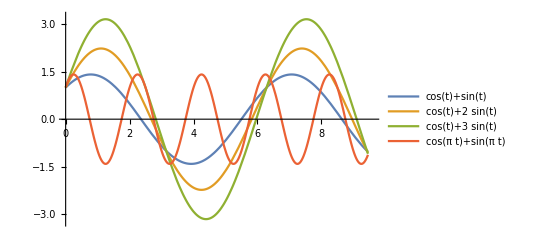

```mathematica
Plot[{Evaluate@Table[ Cos[t]+B Sin[t],{B,1,3}],Cos[π t]+ Sin[π t]},{t,0,3.01π},PlotLegends->"Expressions",PlotRange->{{0,9.6},{-3.25,3.25}}]
```

3.  Frequency. How does the frequency of the harmonic oscillation change if we (i) double the mass, (ii) take a spring of twice the modulus? First find qualitative answers by physics, then look at formulas.

By increasing the mass it will increase inertia, lowering the frequency. By increasing the k-factor, it decreases the range of motion, which speeds up the frequency. Looking at the formula (√(k/m))/(2 π), doubling m reduces the frequency by √2 , and doubling k increases it by the same amount.

5.  Springs in parallel. What are the frequencies of vibration of a body of mass m = 5 kg (i) on a spring of modulus k_1 = 20 nt/m, (ii) on a spring of modulus k_2 = 45 nt/m, (iii) on the two springs in parallel? See the figure below.

For part (i)

Setting the problem up is easy since I already have the mass and the k factor, it being simply

```mathematica
(√(20/5))/(2π)
```

1/π

```mathematica
N[%] (* hertz *)
```

0.31831

For part (ii), with k = 45

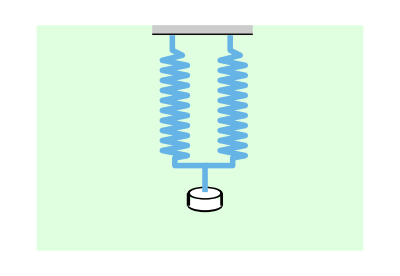

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{6.5,4.5}]},{RGBColor[0.8,0.8,0.8],Rectangle[{2.3,4.3},{4.3,4.5}]},{RGBColor[0.4,0.7,0.9],Thickness[0.01],Line[{{2.7,4.3},{2.7,4},{2.9,3.9},{2.5,3.8},{3,3.7},{2.5,3.6},{3,3.5},{2.5,3.4},{3,3.3},{2.5,3.2},{3,3.1},{2.5,3},{3,2.9},{2.5,2.8},{3,2.7},{2.5,2.6},{3,2.5},{2.5,2.4},{3,2.3},{2.5,2.2},{3,2.1},{2.5,2},{3,1.9},{2.75,1.85},{2.75,1.7},{2.75,1.7},{3.4,1.7}}]},{RGBColor[0.4,0.7,0.9],Thickness[0.01],Line[{{3.85,4.3},{3.85,4},{4.05,3.9},{3.65,3.8},{4.15,3.7},{3.65,3.6},{4.15,3.5},{3.65,3.4},{4.15,3.3},{3.65,3.2},{4.15,3.1},{3.65,3},{4.15,2.9},{3.65,2.8},{4.15,2.7},{3.65,2.6},{4.15,2.5},{3.65,2.4},{4.15,2.3},{3.65,2.2},{4.15,2.1},{3.65,2},{4.15,1.9},{3.9,1.85},{3.9,1.7},{3.35,1.7}}]},{Disk[{3.35,0.9},{0.35,0.13}]},{White,Disk[{3.35,0.94},{0.35,0.13}]},{Disk[{3.35,1.15},{0.35,0.13}]},{White,Disk[{3.35,1.15},{0.3,0.1}]},{Thickness[0.006],Line[{{3.02,1.15},{3.02,0.9}}]},{Thickness[0.005],Line[{{3.68,1.15},{3.68,0.9}}]},{RGBColor[0.4,0.7,0.9],Thickness[0.01],Line[{{3.35,1.7},{3.35,1.17}}]},{Line[{{2.3,4.32},{4.3,4.32}}]}}]
```

```mathematica
(√(90/5))/(2π)
```

3/(√2 π)

```mathematica
N[%]  (* hertz *)
```

0.675237

For part (iii), I am informed by Wikipedia that the spring constants are additive, thus

```mathematica
(√(65/5))/(2π)
```

(√13)/(2 π)

```mathematica
N[%]
```

0.573841

The answers in the green cells above match those of the text.

7.  Pendulum. Find the frequency of oscillation of a pendulum of length L, neglecting air resistance and the weight of the rod, and assuming θ to be so small that Sin[θ] practically equals θ. See the figure below.

```mathematica
ClearAll["Global`*"]
```

I just took the following off a site, https://www.school-for-champions.com/science/pendulum_equations.htm#.XOnkD9NKjOQ. It turns out that the assumption about small θ is necessary, since otherwise the simple-looking problem cannot be solved in closed form. When it is necessary to deal with larger angles, going with NDSolve is apparently a common option.

```mathematica
freq=(√(g/L))/(2π)
```

(√(g/L))/(2 π)

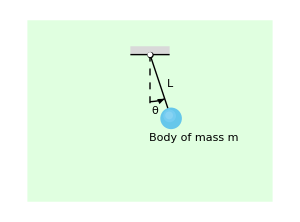

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{5,3.7}]},{RGBColor[0.85,0.85,0.85],Rectangle[{2.1,3},{2.9,3.17}]},{Disk[{2.5,3},0.065]},{Line[{{2.1,3},{2.9,3}}]},{Thick,Line[{{2.5,3},{2.9,1.8}}]},{Dashed,Line[{{2.5,3},{2.5,1.95}}]},{White,Disk[{2.5,3},0.051]},{RGBColor[0.4,0.78,0.92],Disk[{2.93,1.7},0.22]},{Opacity[0.3],RGBColor[0.6,0.85,1],Disk[{2.9,1.75},0.13]},{Opacity[0.15],RGBColor[0.94,0.99,1],Disk[{2.89,1.76},0.08]},{Arrowheads[.041],Arrow[BezierCurve[{{2.5,2.04},{2.7,2.05},{2.8,2.1}}]]},{Text[Style[θ,Medium],{2.6,1.85}]},{Text[Style[L,Medium],{2.9,2.4}]},{Text[Style["Body of mass m",Medium],{3.4,1.3}]}},ImageSize->300]
```

9.  Vibration of water in a tube. If 1 liter of water (about 1.06 US quart) is vibrating up and down under the influence of gravitation in a U-shaped tube of diameter 2 cm, what is the frequency? Neglect friction. See figure below.

```mathematica
ClearAll["Global`*"]
```

I found this same problem developed at https://web.mit.edu/8.01t/www/materials/InClass/WE_Sol_W13D1-2.pdf. The following is a combination of that site and the text answer. The site description supposes that a quickly retracting piston initiates the height offset. I’ve also seen an influx of air pressure described as the initiator in this type of problem. It should be noted that the y-dimension and y=0 level exactly demarcate the halfway point on the excess right side height.

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{5,3.7}]},{RGBColor[0.75,0.95,1],Annulus[{2.5,2},{0.53,0.92},{π,2π}]},{RGBColor[0.2,0.7,0.9],Rectangle[{2.5+0.53,2},{2.5+0.92,2.5}]},{Circle[{2.5,2},0.92,{π,2π}]},{Circle[{2.5,2},0.53,{π,2π}]},{Line[{{2.5-0.92,2},{2.5-0.92,3}}]},{Line[{{2.5+0.92,2},{2.5+0.92,3}}]},{Line[{{2.5-0.53,2},{2.5-0.53,3}}]},{Line[{{2.5+0.53,2},{2.5+0.53,3}}]},{Circle[{1.7766,3},{0.198,0.035}]},{RGBColor[0.75,0.95,1],EdgeForm[Thickness[0.003]],Disk[{1.7766,2},{0.198,0.035}]},{Circle[{3.224,3},{0.198,0.035}]},{RGBColor[0.2,0.7,0.9],EdgeForm[Thickness[0.003]],Disk[{3.224,2},{0.198,0.035}]},{RGBColor[0.2,0.7,0.9],EdgeForm[Thickness[0.003]],Disk[{3.224,2.5},{0.198,0.035}]},{Dashed,Line[{{2.5-0.53,2},{2.5+0.53,2}}]},{Dashed,Line[{{2.5,2.5},{2.5+0.53,2.5}}]},{Dashed,Line[{{2.5,2.25},{3.5,2.25}}]},{Arrowheads[.03],Arrow[{{2.77,2.25},{2.77,2.5}}]},{Text[Style[y,Medium],{2.65,2.39}]},{Text[Style["(y=0)",Medium],{3.75,2.25}]}}]
```

-Graphics-

γ = weight of a cubic meter of water = 1000 kg = 9800 nts force

The problem description gives the information that one liter of water is sloshing around. However, it may not be clear whether that liter comprises the total volume or just the darker-colored, 2y slug. If it was just the slug, then the y dimension could be calculated exactly based on the pipe diameter. However, the text leaves the y length unstated, implying that the liter volume is the whole thing. Anyway, I guess the whole mass is involved in the oscillation. But the π*(0.01)^2*2 y meter^3 plug mass is the cause of the restoring force under examination, that force tagged by the text answer as equal to (a γ y). As for the equation that will result in the frequency, how about

```mathematica
eqn=y''[t]+Subscript[ω, 0]^2 y[t]==0
```

ω_0^2 y[t]+y''[t]==0

The following is the solution to the equation, and though it reassuringly shows the form of SHM, it will not be used to crack the numerical value of the frequency.

```mathematica
sol=DSolve[eqn,y,t]
```

{{y→Function[{t},C[2] Cos[t ω_0]+C[1] Sin[t ω_0]]}}

An equivalence or two from the text answer are unclear to me, so I will switch over to the the online site mentioned above to get a different perspective by grabbing the following.

```mathematica
Subscript[ω, 0]=√((2 g)/L)
```

Working now in meters, cubic meters, and kilograms. Area of liquid surface times length equals volume equivalent to one thousandth of a cubic meter, according to the problem description.

```mathematica
Solve[π*0.01^2*L==0.001,L]
```

{{L→3.1831}}

And using the length I can solve for the frequency “kernel”.

```mathematica
Subscript[ω, 0]=√((2 g)/L)/.{L->3.1831,g->9.80665}
```

2.48228

And convert to numerically expressed frequency.

```mathematica
2.481434947631652/(2π) (* hertz *)
```

0.394933

The answer in the yellow cell above is close to the text answer of 0.4.

11 - 20 Damped motion

11.  Overdamping. Show that for numbered line (7), p. 65 to satisfy initial conditions y(0) = y_0 and v(0) = v_0 we must have c_1 = [(1+α/β)y_0 + v_0/β]/2 and c_2 = [(1-α/β)y_0 - v_0 /β]/2.

13.  Initial value problem. Find the critical motion, numbered line (8), p. 66, that starts from y_0 with initial velocity v_0. Graph solution curves for α = 1, y_0 = 1 and several v_0 such that (i) the curve does not intersect the t-axis, (ii) it intersects it at t = 1, 2, . . . , 5, respectively.

For this one it looks like I’m expected to work directly with numbered line (8),  y[t]=(c_1+c_2 t)ⅇ^(-α t)

It may be as well to let c1 remain equal to 1, and let c2 evolve around it.

```mathematica
Table[Solve[(1+c2 t) ⅇ^-t==0,{c2}],{t,1,5}]
```

{{{c2→-1}},{{c2→-1/2}},{{c2→-1/3}},{{c2→-1/4}},{{c2→-1/5}}}

The consolidated plot below is equivalent to the text answer.

In the first curve in the legend, y_0=1 and α = 1; the second curve has a different y_0 and c1=2, c2=3; the other curves in the legend meet the intersection requirements of the problem description.

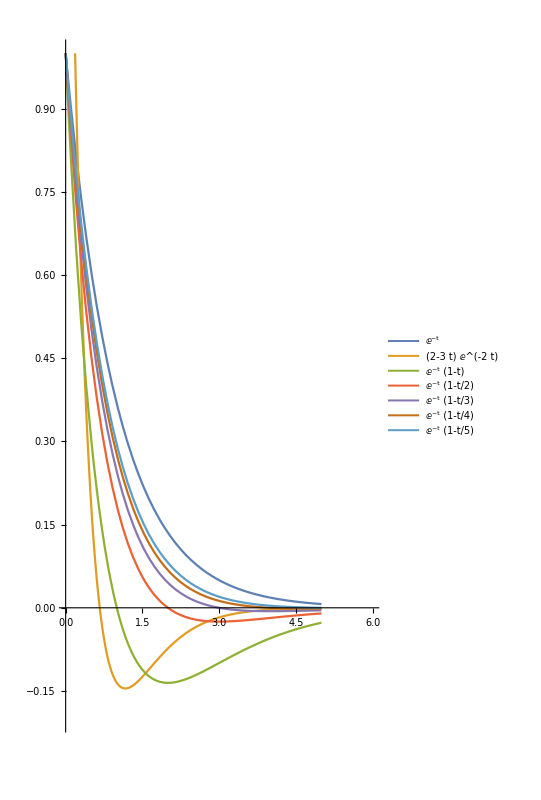

```mathematica
Plot[{ⅇ^-t,(2-3t)ⅇ^(-2t),Evaluate@Table[ {(1+c2*t)*ⅇ^(- t)},{c2,{-1,-1/2,-1/3,-1/4,-1/5}}]},{t,0,5},PlotLegends->"Expressions",PlotRange->{{0,6},{-0.2,1}},AspectRatio->2,PlotStyle->Thickness[0.004]]
```

15.  Frequency. Find an approximation formula for ω^* in terms of ω_0 by applying the binomial theorem in numbered line (9) p. 67, and retaining only the first two terms. How good is the approximation in example 2, section III, p. 68?

Here is an example of using the binomial command in a series setting.

```mathematica
Sum[Binomial[1/2,k](1+x)^k,{k,0,2}]
```

1+(1+x)/2-1/8 (1+x)^2

And an example of a series with binomial persuasion.

```mathematica
Normal[Series[(1+a)^(1/2),{a,0,2}]]
```

1+a/2-a^2/8

In numbered line (9) the focus is on the following expression for ω*, which assents to factoring.

```mathematica
SuperStar[ω]==(k/m-c^2/(4 m^2))^(1/2)==√(k/m)(1-c^2/(4m k))^(1/2)
```

And the factored form can be expressed as a series.

```mathematica
√(k/m)Simplify[Normal[Series[(1-c^2/(4m k))^(1/2),{c,0,2}]]]
```

(1-c^2/(8 k m)) √(k/m)

Applying the particular criteria of example 2, case III, I get

```mathematica
N[(1-c^2/(8 k m)) √(k/m)/.{c->10,m->10,k->90}]
```

2.95833

The number in the green cell above matches the answer in the text.

17.  Underdamping. Determine the values of t corresponding to the maxima and minima of the oscillation y(t) = ⅇ^-t Sin[t]. Check your result by graphing y(t).

```mathematica
ClearAll["Global`*"]
```

I do not understand the text answer regarding Tan[t]. I tried the command ExpToTrig, and Tan didn’t fall out. I just will plug around with some plots.

If a long view is taken of the function, a gigantic spike is seen out around t=-120.

```mathematica
Plot[ⅇ^-t Sin[t],{t,-120,100},PlotRange->All]
```

-Graphics-

```mathematica
N[Maximize[{ⅇ^-t Sin[t],-120<t<-110},t]]
```

{2.26304×10^51,{t→-118.595}}

The adjacent minimum goes into deep water.

```mathematica
N[Minimize[{ⅇ^-t Sin[t],-120<t<-110},t]]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

{-7.57222×10^51,{t→-120.}}

There is another notable maximum close to negative zero.

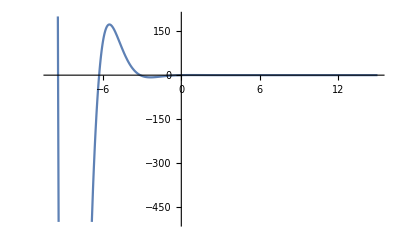

```mathematica
Plot[ⅇ^-t Sin[t],{t,-11,15},PlotRange->{{-10,15},{-500,200}}]
```

```mathematica
N[Maximize[{ⅇ^-t Sin[t],-6<t<4},t]]
```

{172.641,{t→-5.49779}}

And a mild minimum is located to the right of it.

```mathematica
N[Minimize[{ⅇ^-t Sin[t],-6<t<0},t]]
```

{-7.46049,{t→-2.35619}}

Whereas, if I’m interested in the positive domain

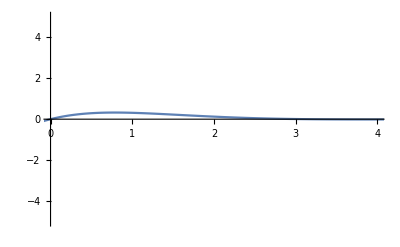

```mathematica
Plot[ⅇ^-t Sin[t],{t,-1,10},PlotRange->{{0,4},{-5,5}}]
```

A little hump is the tallest there is in this neighborhood.

```mathematica
N[Maximize[{ⅇ^-t Sin[t],0<t<10},t]]
```

{0.322397,{t→0.785398}}

And there is a little undercurl for a minimum.

```mathematica
N[Minimize[{ⅇ^-t Sin[t],0<t<10},t]]
```

{-0.013932,{t→3.92699}}

19.  Damping constant. Consider an underdamped motion of a body of mass m = 0.5 kg. If the time between two consecutive maxima is 3 sec and the maximum amplitude decreases to 1/2 its initial value after 10 cycles, what is the damping constant of the system?

```mathematica
ClearAll["Global`*"]
```

Looks like the frequency is 0.3333 hertz.

So I should be able to claim that

```mathematica
SuperStar[ω]== freq(2 π)
```

or

```mathematica
SuperStar[ω]=N[0.3333(2 π)]
```

2.09419

But I also have that

```mathematica
SuperStar[ω]=(k/m-c^2/(4 m^2))^(1/2)
```

from up around problem 15. So if I knew what k was, I could calculate c directly. Aha, Wikipedia to the rescue (article on simple harmonic motion).

```mathematica
Solve[3==2π √(0.5/k),k]
```

{{k→2.19325}}

and I can plug that k-value in

```mathematica
2.09419=(k/m-c^2/(4 m^2))^(1/2)
```

and solve for c.

```mathematica
Solve[(2.19325/0.5-c^2/1)^0.5==2.09419,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-0.029466},{c→0.029466}}

However, the above values of c look somewhat different than the text answer.  The text answer says that c = 0.0231, less than what shows in yellow. But what if I use the text answer c-value to work backward to the k-value.

```mathematica
Solve[(k/0.5-(0.0231)^2/1)^0.5==2.09419,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→2.19308}}

Now, comparing 2.19308 with 2.19325, they do not look that far apart. The ratio

```mathematica
2.19325/2.19308
```

1.00008

looks pretty close. It appears that the damping constant is insanely sensitive to the k-factor.

The following manipulated plot comes from the Wolfram Demonstration, “Forced Oscillator with Damping”, authored by Rob Morris, and uses the values arrived at above. Though I don’t know why, I note that the six input fields on the left need to be dropped down (opened for entry) in order to get the plot trace to show accurately.  When this is done, the first cycle “hump”, running from t=0 to t=2.6, has a leading amplitude of 0.9 and a trailing amplitude of 1.1 (which may be what is meant by an amplitude of 1.0). The tenth cycle “hump” has a leading amplitude of 0.55 and a trailing amplitude of 0.45, with the result that the four half amplitudes cited reveal exactly a 50% reduction in ten cycles, the outcome required by the problem description.

```mathematica
DPPlot[bb_,mm_,kk_,xinit_,AA_,ωω_,tfinal_]:=Module[{},
Clear[t,x,A,ω,k,b,m];
With[{sol=First@NDSolve[{x''[t]+(bb/mm) x'[t]+(kk/mm)x[t]==AA/mm*Cos[ωω t],x'[0]==0,x[0]==xinit},x,{t,0,tfinal}]},Plot[Evaluate[x[t]/.sol],{t,0,tfinal},PlotRange->{{0,tfinal},{-1,1}},ImageSize->{425,350},ImagePadding->{{35,35},{20,40}},AxesLabel->{Style["t",14,Bold,Italic],Style["x(t)",14,Italic,Bold]},GridLines->All,PlotLabel->TraditionalForm[m x''[t]+b x'[t]+k x[t]==A Cos[ω t]]]]]
```

```mathematica
Manipulate[Column[{Switch[plottype,"position",DPPlot[bb,mm,kk,xinit,AA,ωω,time],"phase",DPPhasePlot[bb,mm,kk,xinit,AA,ωω,zoom,time]],Style[Row[{"mass = ",mm,Spacer[20],"|",Spacer[20],"spring constant = ",kk,Spacer[20],"|",Spacer[30],"damping = ",bb}],"Label"],Style[Row[{"driving amplitude = ",AA,Spacer[20],"|",Spacer[20],"driving frequency = ",ωω}],"Label"]},Center],
{{mm,0.5,"mass"},0,10,.01,ImageSize->Tiny},
{{kk,2.193,"spring constant"},0,50,.1,ImageSize->Tiny},
{{bb,0.0294,"damping"},0,5,.01,ImageSize->Tiny},
{{xinit,0,"initial position"},0,10,ImageSize->Tiny},Delimiter,"forcing function",{{AA,1,"amplitude"},0,10,.05,ImageSize->Tiny},{{ωω,0.333,"frequency",ImageSize->Tiny},0,2Pi,.01,ImageSize->Tiny},
Delimiter,
{{plottype,"position","plot type"},{"position","phase"}},{{zoom,10},.5,20,ImageSize->Tiny,Enabled->plottype=="phase"},
Delimiter,
{{time,50},10,200,ImageSize->Tiny},
SaveDefinitions->True,AutorunSequencing->{2,3,5}]
```